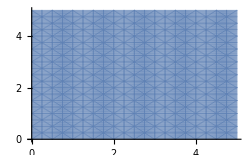

-Graphics-

```mathematica
data=Import["/home/majernik/Programming/C++/FEM3/kut.CSV","CSV"];
columnX = data[[All, 1]];
columnY = data[[All, 2]];
columnZ = data[[All, 3]];
columnScalar = data[[All, 4]];

plotData= Transpose@{columnX, columnY, columnScalar};
dataPoints = Transpose@{columnX, columnY};
ListPlot[dataPoints]
ListDensityPlot[plotData,PlotLegends->Automatic ,ColorFunction->(ColorData["Rainbow"][Rescale[#,{30,110}]]&),ColorFunctionScaling->False,PlotRange->{30,110}]
```